## Startup

```mathematica
libDir = NotebookDirectory[] <> "lib\\";
```

```mathematica
Get[libDir <> "competitionFunctions.wl"];
```

```mathematica
Get[libDir <> "modelOptimization.wl"];
```

## Import data

### Page views, train_2.csv

```mathematica
(*(* Convert to memory-dump format.  Takes 20 minutes *)
AbsoluteTiming[
	{pages, dates, views} = importTraffic[DATADIR <> "train_2.csv"];
]
Export[DATADIR <> "train_2.mx", {pages, dates, views}];*)
```

```mathematica
{pages, dates, views} = Import[DATADIR <> "train_2.mx"];
```

```mathematica
(*Column[Map[ListPlot[#, Joined->True, AspectRatio->.1, ImageSize->Full]&, views[[-90;;-60]]]]*)
```

### Submission keys, key_2.csv

```mathematica
(*(* Convert to memory-dump format.  Takes 3 minutes *)
AbsoluteTiming[
	keys = importKeys[DATADIR <> "key_2.csv"];
]
Export[DATADIR <> "key_2.mx", keys];*)
```

```mathematica
keys = Import[DATADIR <> "key_2.mx"];
```

```mathematica
Length[keys]
Length[pages]*62
```

8993906

8993906

## Calculate indicators (compiled)

```mathematica
getIndicators[past_, fitPars_] := Block[
	{
		offset,end,medianEndLength,medianListInc,medianListN,
		logp1,yearBasis,yearBasisInverse,polyBasisShort,polyBasisLong,out,
		indicatorPars 
	},

	offset = fitPars[["offset"]];
	end = fitPars[["end"]];
	medianEndLength = fitPars[["medianEndLength"]];
	medianListInc = fitPars[["medianListInc"]];
	medianListN = fitPars[["medianListN"]];
	
	logp1 = Map[If[#<0, NULLVALUE, Log[#+1.]]&, past, {2}];	

	yearBasis = polyBasis[fitPars[["yearlyPastOrder"]], end-offset+1];
	
	indicatorPars = {offset,end,medianEndLength,medianListInc,medianListN};
	out = getIndicatorsInternal[logp1, yearBasis, PseudoInverse[yearBasis], indicatorPars];
	out = Map[separateIndicators, out];
	out

];
```

```mathematica
medianNonNull = Compile[{{list, _Real, 1}}, Module[
	{NULLVALUE=-128,positive},
	
	positive = Select[list, #>NULLVALUE&];
	If[positive=={}, 0, Median[positive]]

],
	CompilationTarget->"C"
];
```

```mathematica
getIndicatorsInternal = Compile[{{logp1, _Real, 1}, {yearBasis, _Real, 2}, {yearBasisInverse, _Real, 2}, {indicatorPars, _Integer, 1}}, 
	 
Module[

	{
		NULLVALUE=-128,
		offset, end, medianEndLength, medianListInc, medianListN,
		length,out,nonNull,numNonNull,last,zeroNull,medianEnd,medianAll,
		min,take,medianList,
		weekdays,weekMedians,weekdaysCentered,weekPattern,weekAmplitude,
		padding,mf,medianFiltered,lastYear,yearBefore,yearDiff=1.,numerator,denominator,lastYearFuture,
		polyLastYearFuture={0.,0.,1.},polyShort={0.,0.,0.},polyLong={0.,0.,0.}
	},
	
	{offset, end, medianEndLength, medianListInc, medianListN} = indicatorPars;

	length = Length[logp1];
	
	nonNull = Select[logp1, #>NULLVALUE&];
	numNonNull = Length[nonNull];
	last = If[numNonNull==0, 0., nonNull[[-1]]];
	
	zeroNull = Map[If[#==NULLVALUE, 0., #]&, logp1];
	medianEnd = Median[Take[zeroNull, -medianEndLength]];
	medianAll = Median[zeroNull];
	
	(* Get medians of histories of various lengths *)
	take = medianListInc^Range[medianListN];
	If[Max[take]>length, 
		take = Floor[take/Max[take]*length];
		take = Map[If[#>length, length, #]&, take];
		take = Map[If[#<1, 1, #]&, take];
	];
	take = -take;
	medianList = Map[Median[Take[zeroNull, #]]&, take];

	(* Get week pattern *)
	weekdays = Map[Reverse, Partition[Reverse[logp1], 7]];
	weekMedians = Map[medianNonNull, weekdays];
	weekdaysCentered = Table[
		If[weekdays[[i,j]]==-1, -1, weekdays[[i,j]]-weekMedians[[i]]]
	, 
		{i,1,Length[weekdays]}, 
		{j,1,7}
	];
	weekPattern = Map[medianNonNull, Transpose[weekdaysCentered]];

	(* Separate weekPattern into amplitude and pattern *)
	(* Allows a small degree of trainability (amplitude can be adjusted later by model) *)
	(* Set amplitude to zero if it is << Log[1+1], to avoid later numerical instability, divide-by-zero.  *)
	weekPattern -= Mean[weekPattern];
	weekAmplitude = StandardDeviation[weekPattern];
	If[weekAmplitude < 0.1,
		weekAmplitude = 0.;
		weekPattern *= 0;
	,
		weekPattern /= weekAmplitude;
	];

	(* Get data after 1 year ago *)
	(* Helps predict behavior for pages about religious holidays, sporting events, etc.*)
	If[Length[nonNull]>470, 
		(* Median filter, width 7 *)
		padding = Table[-1., {3}];
		mf = Partition[Join[padding, nonNull, padding], 7, 1];
		medianFiltered = Map[medianNonNull, mf];

		(* Get recent data (lastYear) and data preceding one year ago (yearBefore) *)
		lastYear = medianFiltered[[-365;;-1]];
		yearBefore = medianFiltered[[1;;-366]];

		(* Make lastYear and yearBefore the same length, while maintaining alignment *)
		If[Length[yearBefore]>365, yearBefore = Take[yearBefore, -365]];
		If[Length[yearBefore]<365, lastYear = Take[lastYear, -Length[yearBefore]]];

		(* Get a measure of the difference between the histories *)
		(* Scaled to (0,1).  0: no difference, 1: maximum difference *)
		lastYear -= Median[lastYear];
		yearBefore -= Median[yearBefore];
		numerator = Norm[lastYear-yearBefore];
		denominator = Norm[lastYear]+Norm[yearBefore];
		yearDiff = If[denominator<10.^-5, 1., numerator/denominator];

		(* Get polynomial expansion of data following one year ago *)	
		lastYearFuture = medianFiltered[[(-365+offset);;(-365+end)]];
		lastYearFuture -= Median[medianFiltered[[-395;;-365]]];
		polyLastYearFuture = fastMedianRegression[lastYearFuture, yearBasis, yearBasisInverse, 10^-5];

	];

	(* Return results matrix *)
	(* First column is length of result *)
	(* All rows in matrix are of same length, so shorter results are padded right *)
	out = Table[0., {9}, {20}];
	out[[1,2]] = numNonNull;
	out[[2,2]] = last;
	out[[3,2]] = medianEnd;
	out[[4,1]] = Length[weekPattern];  out[[4,2;;Length[weekPattern]+1]] = weekPattern;
	out[[5,2]] = weekAmplitude;
	out[[6,2]] = yearDiff;
	out[[7,1]] = Length[polyLastYearFuture];  out[[7,2;;Length[polyLastYearFuture]+1]] = polyLastYearFuture;
	out[[8,2]] = medianAll;
	out[[9,1]] = Length[medianList]; out[[9,2;;Length[medianList]+1]] = medianList;

	out

], 
	CompilationTarget->"C", 
	RuntimeAttributes->{Listable}, Parallelization->True, 
	CompilationOptions->{"InlineExternalDefinitions" -> True}
];
```

```mathematica
separateIndicators[indicatorsMatrix_] := Block[{names,out},
	names = {"numNonNull","last","medianEnd","weekPattern","weekAmplitude","yearDiff","polyLastYearFuture","medianAll","medianList"};
	out = Map[If[#[[1]]==0., #[[2]], Take[#, 2;;(2+#[[1]]-1)]]&, indicatorsMatrix];
	out = Table[names[[i]]->out[[i]], {i,1,Length[out]}];
	out = Apply[Association, out];
	out
];
```

## Functions for fitting and predicting

```mathematica
standardizer[vectors_] := Block[
	{mean,vecs,stdev,u,w,v,subspace},
	
	mean = Mean[vectors];
	vecs = Map[#-mean&, vectors];
	stdev = StandardDeviation[vecs];
	stdev = Map[If[#==0., 0., 1/#]&, stdev];
	vecs = Map[#*stdev&, vecs];

	With[
		{m=mean, s=stdev}, 
		Map[((#-m)*s)&, #]&
	]
];
```

```mathematica
modelFit[indicators_, toPredict_, fitPars_] := Block[
	{
		offset, end, highVolumeMin, highVolumeOrder, highVolumeNbrs, 
		yearlyMaxDiff, yearlyFutureOrder, highVolumeCrossover, yearlyCrossover, 		
		modelVariables,highVolumeMask,x,y,mean,
		highVolumeBasis,highVolumeBasisInverse,highVolumeYLowD,highVolumeNearest,highVolumeStandardizer,
		yearlyPatternMask,yearlyIndicators,yearlyBasis,yearlyBasisInverse,yearlyYLowD,yearlyModel
	},

	offset = fitPars[["offset"]];
	end = fitPars[["end"]];
	
	highVolumeMin = fitPars[["highVolumeMin"]];
	highVolumeOrder = fitPars[["highVolumeOrder"]];
	highVolumeNbrs = fitPars[["highVolumeNbrs"]];

	yearlyMaxDiff = fitPars[["yearlyMaxDiff"]];
	yearlyFutureOrder = fitPars[["yearlyFutureOrder"]];

	highVolumeCrossover = fitPars[["highVolumeCrossover"]];
	yearlyCrossover = fitPars[["yearlyCrossover"]];

	(*****************************************************************)
	(* Fit model based on polynomial regression of high-volume pages *)
	(*****************************************************************)

	highVolumeMask = Map[#≥highVolumeMin&, indicators[[All, "medianAll"]]];
	x = Pick[indicators[[All, "medianList"]], highVolumeMask];
	y = Pick[Log[ReplaceAll[toPredict, NULLVALUE->0.]+1.], highVolumeMask];

	(* Subtract mean *)
	mean = Pick[indicators[[All, "medianEnd"]], highVolumeMask];  (*x[[All, 4]];*) (*Map[Mean, x];*)
	x -= mean;
	y -= mean;

	(* Expand y in polynomial basis *)
	highVolumeBasis = polyBasis[highVolumeOrder, Length[y[[1]]]];
	highVolumeBasisInverse = PseudoInverse[highVolumeBasis];
	highVolumeYLowD = fastMedianRegression[y, highVolumeBasis, highVolumeBasisInverse, 10.^-4];
(*
	(* Standardize x *)
	highVolumeStandardizer = standardizer[x];
	x = highVolumeStandardizer[x];
	*)
	(* Get nearest neighbor function for estimating yLowD in terms of x *)
	highVolumeNearest = Nearest[x->Range[Length[x]]];
	
	(*************************************************************************)
	(* Fit model based on polynomial regression of pages with yearly pattern *)
	(*************************************************************************)

	yearlyPatternMask = Map[#<yearlyMaxDiff&, indicators[[All,"yearDiff"]]];
	yearlyIndicators = {"medianEnd","polyLastYearFuture"};
	x = Pick[indicators, yearlyPatternMask][[All, yearlyIndicators]];
	x = Map[Flatten[Values[#]]&, x];
	y = Pick[Log[ReplaceAll[toPredict, NULLVALUE->0.]+1.], yearlyPatternMask];

	(* Expand y in polynomial basis *)
	yearlyBasis = polyBasis[yearlyFutureOrder, Length[y[[1]]]];
	yearlyBasisInverse = PseudoInverse[yearlyBasis];
	yearlyYLowD = fastMedianRegression[y, yearlyBasis, yearlyBasisInverse, 10.^-4];

	(* Fit linear model:  x.yearlyModel = yearlyYLowD *)
	yearlyModel = PseudoInverse[x].yearlyYLowD;

	modelVariables = Join[fitPars, <|
		"highVolumeY" -> highVolumeYLowD,
		"highVolumeNearest" -> highVolumeNearest,
		"highVolumeNbrs" -> highVolumeNbrs,
		"highVolumeBasis" -> highVolumeBasis,
		(*"highVolumeStandardizer" -> highVolumeStandardizer,*)
		"yearlyIndicators" -> yearlyIndicators,
		"yearlyModel"-> yearlyModel,
		"yearlyBasis" -> yearlyBasis
	|>];

	With[{mv = modelVariables}, modelPredict[#, mv]&]
];
```

```mathematica
(* Get blend predictions using crossover *)
crossOver[x_, {min_, max_}] := If[x<min, 0, If[x>max, 1, Rescale[x, {min, max}, {0,1}]]];

blender[blendIndicators_, highVolumeCrossover_, yearlyCrossover_] := Block[{portionYearly,portionMedian,portionHighVolume,out},

	portionMedian = 1-crossOver[blendIndicators[[2]], highVolumeCrossover];
	portionYearly = 1-crossOver[blendIndicators[[1]], yearlyCrossover];
	portionHighVolume = 1 - (portionYearly + portionMedian);
	
	out = {portionMedian, portionHighVolume, portionYearly};
	out = Clip[out, {0,1}];
	out /= Total[out];
	
	out = Prepend[out, 1];
	
	out
];
```

```mathematica
modelPredict[indicators_, modelVariables_] := Block[
	{
		weekPattern,offset,end,
		y,futLength,medianPrediction,
		x,mean,hvY,hvNearest,hvNbrs,highVolumePrediction,
		yearlyPrediction,
		toBlend,blendIndicators,
		highVolumeCrossover,yearlyCrossover,
		blendingRatios,out,i
	},

	(*************************************************
		Get prediction of weekly pattern              
		(to be added to mixture of predictions below) 
	**************************************************)
	offset = modelVariables[["offset"]];
	end = modelVariables[["end"]];
	weekPattern = indicators[[All, "weekPattern"]] * indicators[[All, "weekAmplitude"]];
	weekPattern = Table[Flatten[Table[weekPattern[[i]], {Ceiling[end/7+1]}]], {i,1,Length[weekPattern]}];
	weekPattern = weekPattern[[All, offset;;end]];
	
	(*****************************************)
	(* Get prediction based on simple median *)
	(******************************************)
	y = indicators[[All, "medianEnd"]];
	futLength = Length[modelVariables[["yearlyBasis"]][[1]]];
	y = Table[y[[i]], {i,1,Length[y]}, {futLength}];
	medianPrediction = y;
	
	(**********************************************************************)
	(* Get prediction based on polynomial regression of high-volume pages *)
	(**********************************************************************)
	
	x = indicators[[All,"medianList"]];
	mean = indicators[[All,"medianEnd"]];
	x -= mean;
	(*x = modelVariables[["highVolumeStandardizer"]][x];*)
	{hvY, hvNearest, hvNbrs} = Values[modelVariables[[{"highVolumeY", "highVolumeNearest", "highVolumeNbrs"}]]];
	y = Map[Mean[hvY[[hvNearest[#, hvNbrs]]]]&, x];
	y = y.modelVariables[["highVolumeBasis"]];
	y += mean;
	highVolumePrediction = y;

	(******************************************************************************)
	(* Get prediction based on polynomial regression of pages with yearly pattern *)
	(******************************************************************************)

	x = indicators[[All, modelVariables[["yearlyIndicators"]]]];
	x = Map[Flatten[Values[#]]&, x];
	y = x.modelVariables[["yearlyModel"]].modelVariables[["yearlyBasis"]];
	yearlyPrediction = y;

	(****************************************************************************
		Blend predictions so that low volume pages get median prediction, 
		yearly pattern pages get their prediction, 
		and everything else gets polynomial regression on high-volume pages 
	***************************************************************************)
	
	(* Get matrix of patterns to blend.  Dimensions = (sample, model, day) *)
	toBlend = Transpose[{weekPattern, medianPrediction, highVolumePrediction, yearlyPrediction}];

	(* Use this to investigate methods of determining blending ratios *)
	(* Code is in notebook /2017-09-02c Investigate fitting methods for low, high volume/polynomial regression for high volume pages.nb *)
	(*Return[toBlend];*) 

	(* Get the indicators that will be used to determine how to blend the model predictions *)
	blendIndicators = indicators[[All, {"yearDiff", "medianAll"}]];
	blendIndicators = Map[Flatten[Values[#]]&, blendIndicators];

	(* Get the crossover definitions *)
	highVolumeCrossover = Values[modelVariables[[{"highVolumeCrossoverMin","highVolumeCrossoverMax"}]]];
	yearlyCrossover = Values[modelVariables[[{"yearlyCrossoverMin","yearlyCrossoverMax"}]]];

	(* Get the blending ratios by applying the crossovers to the indicators *)
	blendingRatios = Map[blender[#, highVolumeCrossover, yearlyCrossover]&, blendIndicators];

	(* Apply the blending ratios *)
	out = Table[0., {Length[toBlend]}, {Length[toBlend[[1,1]]]}];
	For[i=1, i≤Length[out], i++,
		out[[i]] = blendingRatios[[i]].toBlend[[i]];
	];

	(* Return prediction *)
	Round[Clip[Exp[out]-1, {0, Infinity}]]

];
```

## Test fit and predict

```mathematica
fitPars = <|

(* Future positions *)
	"offset"->2, 
	"end"->63,

(* Indicator calculation parameters *)
	"medianEndLength"->35,
	"medianListInc"->2, 
	"medianListN"->7,
	"yearlyPastOrder"->2,
		
(* Fitting/predicting parameters *)
	"highVolumeMin"->4, 
	"highVolumeOrder"->1, 
	"highVolumeNbrs"->200, 
	"yearlyMaxDiff"->0.4, 
	"yearlyFutureOrder"->2, 
	"highVolumeCrossoverMin"->0.5,
	"highVolumeCrossoverMax"->3.5,
	"yearlyCrossoverMin"->0.2,
	"yearlyCrossoverMax"->0.8

|>;
```

```mathematica
f = views[[All,1;;-64]];
t = views[[All,-62;;-1]];

ch = RandomChoice[Range[Length[f]], 5000];
(*ch = All;*)

f = f[[ch]];
t = t[[ch]];
```

```mathematica
AbsoluteTiming[
	ind = getIndicators[f, fitPars];
]
```

{2.5271,Null}

```mathematica
AbsoluteTiming[
	pf = modelFit[ind, t, fitPars];
]
```

{0.769627,Null}

```mathematica
AbsoluteTiming[
	pred = pf[ind];
]
```

{1.18659,Null}

```mathematica
AbsoluteTiming[
	smape[pred, t]
]
```

{0.0558983,37.0267}

```mathematica
AbsoluteTiming[
	res = crossValidate[f, t, fitPars, getIndicators, modelFit[#1, #2, fitPars]&, smape, 5][[1]];
]
Mean[res]
```

{6.77232,Null}

37.0991

## Get dataset with random stop days

```mathematica
fitPars = <|

(* Future positions *)
	"offset"->3, 
	"end"->64,

(* Indicator calculation parameters *)
	"medianEndLength"->26,
	"medianListInc"->2,
	"medianListN"->10,
	"yearlyPastOrder"->2,

(* Fitting/predicting parameters *)
	"highVolumeMin"->1, 
	"highVolumeOrder"->1, 
	"highVolumeNbrs"->150, 
	"yearlyMaxDiff"->0.4, 
	"yearlyFutureOrder"->2, 
	"highVolumeCrossoverMin"->-5,
	"highVolumeCrossoverMax"->1.5,
	"yearlyCrossoverMin"->0.15,
	"yearlyCrossoverMax"->0.7

|>;
```

```mathematica
{from, to} = sampleHistory[views, fitPars];
```

```mathematica
AbsoluteTiming[
	res = crossValidate[from, to, fitPars, getIndicators, modelFit[#1, #2, fitPars]&, smape, 10][[1]];
]
Mean[res]
```

{518.877,Null}

38.7563

## Ensemble

```mathematica
fitPars = <|

(* Future positions *)
	"offset"->3, 
	"end"->64,

(* Indicator calculation parameters *)
	"medianEndLength"->26,
	"medianListInc"->2,
	"medianListN"->10,
	"yearlyPastOrder"->2,

(* Fitting/predicting parameters *)
	"highVolumeMin"->1, 
	"highVolumeOrder"->1, 
	"highVolumeNbrs"->150, 
	"yearlyMaxDiff"->0.3, 
	"yearlyFutureOrder"->2, 
	"highVolumeCrossoverMin"->-5,
	"highVolumeCrossoverMax"->1.5,
	"yearlyCrossoverMin"->0.15,
	"yearlyCrossoverMax"->0.7

|>;
```

```mathematica
ensemble = {};

For[en=1, en≤10, en++,

	Print[DateString[], "    ", en, "/", 10];
	
	(* Train model *)
	{from, to} = sampleHistory[views, fitPars];
	ind = getIndicators[from, fitPars];
	model = modelFit[ind, to, fitPars];
	
	(* Apply to recent data *)
	ind = getIndicators[views, fitPars];
	predictions = model[ind];
	
	AppendTo[ensemble, predictions];

];
```

Mon 1 Jan 2018 14:02:26    1/10

Mon 1 Jan 2018 14:08:50    2/10

Mon 1 Jan 2018 14:15:17    3/10

Mon 1 Jan 2018 14:21:46    4/10

Mon 1 Jan 2018 14:28:07    5/10

Mon 1 Jan 2018 14:34:37    6/10

Mon 1 Jan 2018 14:41:11    7/10

Mon 1 Jan 2018 14:47:48    8/10

Mon 1 Jan 2018 14:54:21    9/10

Mon 1 Jan 2018 15:00:58    10/10

```mathematica
Dimensions[ensemble]
```

{10,145063,62}

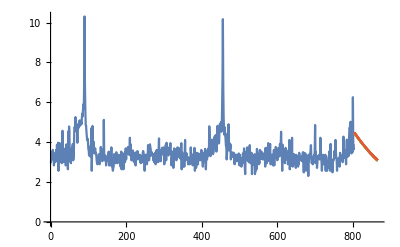

```mathematica
n = RandomChoice[Range[Length[views]]];
f = views[[n]];
p = ensemble[[All,n]];
ensemblePlot[f, p]
```

## Export

```mathematica
ensembleMean = Mean[ensemble];
```

```mathematica
exportSubmission[ensembleMean, pages, keys, "2017-09-10", fitPars[["offset"]], fitPars[["end"]]];
```

Dates from 2017-09-13 to 2017-11-13